# Solving the Schrodinger equation for finite potentials: from atoms to molecules and solids

Authors : Angel Salazar
Schoool of Physical Sciences and Nanotechnolgy, Yachay Tech University, Urcuuqui-Ecuador

## The infinite potential well

The symbols we will use: for energy  ℰ, φ, ℏ,

```mathematica
eq=-ℏ^2/(2 m) φ''[x]==ℰ φ[x]
```

-(ℏ^2 φ''[x])/(2 m)==ℰ φ[x]

```mathematica
DSolve[eq,φ[x],x]
```

{{φ[x]→C[1] Cos[(√2 √m x √ℰ)/ℏ]+C[2] Sin[(√2 √m x √ℰ)/ℏ]}}

From boundary condition we see that c1=0 since φ[x=0]=c1=0

Solve[]

```mathematica
Solve[(√2 √m x √ℰ)/ℏ==n π ,ℰ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ℰ→(n^2 π^2 ℏ^2)/(2 m x^2)}}

```mathematica
Sin[(√2 √m x √ℰ)/ℏ]/.ℰ->(n^2 π^2 ℏ^2)/(2 m)
```

Sin[(√m π x √((n^2 ℏ^2)/m))/ℏ]

```mathematica
Integrate[c2^2 Sin[(n π x)/a]^2,{x,0,a}]
```

1/4 a c2^2 (2-Sin[2 n π]/(n π))

```mathematica
Solve(1/4 a c2^2 (2-Sin[2  0 π]/(n π))==1,c2)
```

{{c2→-(√2)/(√a)},{c2→(√2)/(√a)}}

Let’s t define the wavefunction , using the piecewise function ψ

```mathematica
v[x_]:=Piecewise[{{50, x <0}, {0, 0<=x<=a}, {50, x>a}}]
φ[x_, n_]:= Piecewise[{{0, x <0}, {(√2)/(√a) Sin[(n π x)/a], 0<=x<=a}, {0, x>a}}]
```

```mathematica
Manipulate[
Plot[{φ[x,n]+(n^2 π^2 ℏ^2)/(2 a^2 m), φ[x,n]^2+(n^2 π^2 ℏ^2)/(2 a^2 m),v[x],(n^2 π^2 ℏ^2)/(2 a^2 m)}/.{ℏ->1,m->1,n->nval,a->aval}//Evaluate,
{x,-0.1,aval+0.1},
PlotRange->{{-0.1, 3},{-0.1, 45}},
Filling->{2->{4}},
PlotStyle->{Blue,Green,{Red,Thickness[0.01]},Black},
ImageSize->200,
AspectRatio->1,
Ticks->{Automatic,None},
Exclusions->None],
{{aval,1.5},1,3},{{nval,1},1,5,1},ControlPlacement->Right]
```

## Single finite potential well: model of a single atom

Let’s define the potential:

```mathematica
v[x_]:=Piecewise[{{v0, x<-a/2}, {0, -a/2<x<a/2}, {v0, x>a/2}}]
```

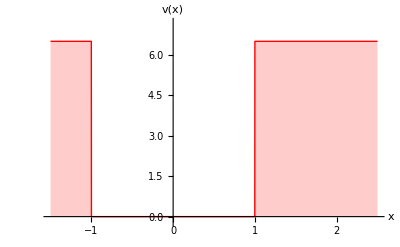

```mathematica
la=2(*bohr*);
vpot=6.5(*Subscript[E, h]*);
Plot[v[x]/.{v0->vpot,a->la},{x,-la+0.5,la+0.5},
AxesLabel->{"x","v(x)"},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,7.2}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]
```

## SOlving the Schrodinger equation in a.u.

```mathematica
eq1=-1/2 ϕ1''[x]+v0 ϕ1[x]==ℰ ϕ1[x]
```

v0 ϕ1[x]-ϕ1''[x]/2==ℰ ϕ1[x]

```mathematica
DSolve[eq1,ϕ1[x],x]
```

{{ϕ1[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]+ⅇ^(-√2 x √(v0-ℰ)) C[2]}}

```mathematica
eq2=-1/2 ϕ2''[x]==ℰ ϕ2[x]
```

-1/2 ϕ2''[x]==ℰ ϕ2[x]

```mathematica
DSolve[eq2,ϕ2[x],x]
```

{{ϕ2[x]→C[1] Cos[√2 x √ℰ]+C[2] Sin[√2 x √ℰ]}}

```mathematica
eq3=-1/2 ϕ3''[x]+v0 ϕ3[x]==ℰ ϕ3[x]
```

v0 ϕ3[x]-ϕ3''[x]/2==ℰ ϕ3[x]

```mathematica
DSolve[eq3,ϕ3[x],x]
```

{{ϕ3[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]+ⅇ^(-√2 x √(v0-ℰ)) C[2]}}

Let’s define α=√(2(v0-ℰ)) and β =√(2 ℰ),ϕ

```mathematica
Do[Subscript[c,i]=.,{i,4}];
Do[Subscript[ϕ,i]=.,{i,3}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
ϕ2[x_]:=Subscript[c, 2] Cos[β x]+c
```